```mathematica
k0 = Pi ;
EnergFunc[k_]:=3/2  DiracDelta[k-k0];
RhsFunc[r_]=Integrate[2*EnergFunc[k] Sin[k*r]/(k r),{k, 0, Infinity}];
RhsFunc[0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/π encountered.

Indeterminate

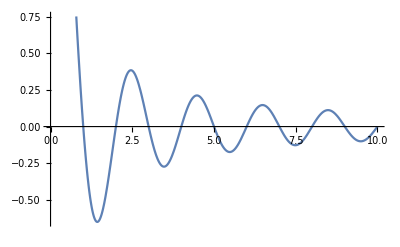

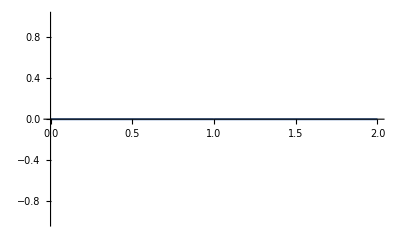

```mathematica
Plot[RhsFunc[r],{r,0,10}]
Plot[DiracDelta[k - 1], {k, 0, 2}]
```

```mathematica
v0=1;
EnergFuncGauss[k_]=16 * (2 / Pi)^(1/2) * v0^2 k^4 k0^(-5) E^(- 2 k^2 / k0^2);
```

```mathematica
RhsFunc[r_]=Integrate[EnergFuncGauss[k] Sin[k*r]/(k r),{k, 0, Infinity}];
```

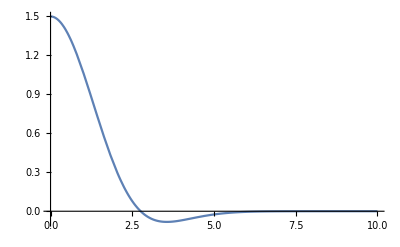

```mathematica
Plot[RhsFunc[r],{r,0,10},PlotRange->Full]
```